Adjudication on

# Exchange energy for two closed shells generated by a bare Coulomb potential energy -Ze^2/r in the limit of large Z, in two dimensions

M.L. Glasser, N.H. March, and L.M. Nieto

## Report

In this paper the authors perform an analytic calculation of the idempotent Dirac density matrix γ(r, r') generated by two closed shells for the bare Coulomb potential -Ze^2/r and the exchange energy density ϵ_x(r).

I have read the paper and the three referee reports. Each report is rather short, but raises important criticisms. In particular, the presentation lacks physical motivation; as the second referee points out,

…two-dimensional artificial atoms (or quantum dots) are obtained through the lateral confinement of a high-mobility modulation-doped two-dimensional electron gas in a semi-conductor hetero-structure. The lateral confinement is very strong, so that the Coulomb potential is probably not a good model for the confining potential.

The third referee notes that the importance of this paper

…is substantially reduced due to its assumption of the large nuclear charge limit.

The first referee argues that, since the wavefunctions and energies are explicitly available, computing the reduced density matrix and the exchange energy is straightforward. This is certainly true computationally. However, the stated goal of this paper—only partially achieved—is an analytic derivation of the exchange energy density, at least for the coulomb potential. As is shown below, it is straightforward to implement, check, (and extend) all the derivations in this paper using a computer algebra system (CAS), and to express the exchange energy/unit energy in closed form.

The paper concludes with a brief exploration of whether the entire density matrix for closed shells can be determined by its s-state component alone, and the observation that the (2D Coulomb) Green's function is expressible in terms of scalar variables. However, this analysis is restricted to the Coulomb potential.

Unfortunately, this paper lacks coherence and its quality is marred by a number of typographical errors and notational issues; apart from the issue identified by the second referee, in Section 2 I found errors in equation (5), the definition of E, and the normalization of ψ_(n,l)(r,ϕ) in equation (10), along with and the appearance of (an undefined) β.

In conclusion, there is insufficient original work in this paper to recommend publication in J Phys A.

## Comments

I believe that computations presented in articles must be reproducible and derivations should be automated (where possible, using a CAS). Authors should provide their data and documented software sources, allowing reproducible computation of numerical and algebraic results from the input data. This would enable referees (and readers) to quickly test and verify the results presented. Too much time is wasted checking flawed derivations and reproducing and analysing simulated data. The idea of reproducible computation is popular in the statistics and wavelet theory communities but the adoption of reproducible research practice by journals, computational scientists, and engineers has been slow. Partially, this is caused by difficult and inadequate tools. However, using Mathematica, I have reproduced every computation in all the papers that I've reviewed (and read) over the last 5 years.

I have used Mathematica for the following derivations so that all results can be verified directly. The reason for including this detailed CAS derivation is four-fold:

List. if the derivation is trivial, the paper should not be published;

List. implementation in a CAS forces a clear and consistent notation without hidden assumptions;

List. many published papers would benefit from an accompanying CAS derivation, enabling referees (and adjudicators) to quickly check the analysis and computations;

List. it would simplify the extension or adaptation of the published work to related problems.

## Solving the Schrödinger equation

### Radial Schrödinger Equation

In 2D the Laplacian reads

```mathematica
Δ(ψ_):=(∂^2 ψ)/(∂r^2)+1/r(∂ψ)/(∂r)+1/r^2(∂^2 ψ)/(∂ϕ^2)
```

and the Hamiltonian is

```mathematica
ℋ(ψ_):=-ℏ^2/(2m)Δ(ψ)+𝒱(r)ψ
```

Using separation of variables,

```mathematica
Ψ(r_,ϕ_):=R(r)Φ(ϕ)
```

with the (normalised) angular functions,

```mathematica
Φ(ϕ_):=1/(√(2π))ⅇ^(ⅈ l ϕ)
```

and the Coulomb potential,

```mathematica
𝒱(r_):=-(Z e^2)/r
```

the radial Schrödinger equation for R(r) reads (correcting equation (5),

```mathematica
radialSE=Collect[-(2m)/ℏ^2(ℋ(Ψ(r,ϕ))-ℰ Ψ(r,ϕ))/(Φ(ϕ))//Simplify,R(r),Expand]==0
```

R(r) ((2 e^2 m Z)/(r ℏ^2)-l^2/r^2+(2 m ℰ)/ℏ^2)+R''(r)+(R'(r))/r==0

### Natural Units

It is advantageous to work in natural units (m==ℏ==e==1). The natural unit of length is

```mathematica
𝒶=ℏ^2/(m e^2);
```

and the natural unit of energy is e^2/𝒶.

Rescale lengths r→𝒶 ρ and energies ℰ→(e^2/𝒶)ℰ̄, and put R(r)→ℛ(ρ).

```mathematica
radialSE=Collect[𝒶^2 radialSE/.{r->𝒶 ρ,ℰ->e^2/𝒶 ℰ̄}/.R->(r↦ ℛ(r/𝒶)),ℛ(ρ),Expand]
```

ℛ(ρ) (2 ℰ̄-l^2/ρ^2+(2 Z)/ρ)+ℛ''(ρ)+(ℛ'(ρ))/ρ==0

Introduce ℰ̄→-Z^2/(2 𝒩^2),

```mathematica
radialSE=radialSE/.ℰ̄->-Z^2/(2 𝒩^2)
```

ℛ(ρ) (-l^2/ρ^2-Z^2/𝒩^2+(2 Z)/ρ)+ℛ''(ρ)+(ℛ'(ρ))/ρ==0

### Radial Eigenfunctions

The general solution is immediate:

```mathematica
solution=ℛ(ρ)/.First@DSolve[radialSE,ℛ,ρ]//FullSimplify//ExpandAll
```

c_1 ρ^l ⅇ^(-(ρ Z)/𝒩) l-𝒩+1/22 l+1(2 Z ρ)/𝒩+c_2 ρ^l ⅇ^(-(ρ Z)/𝒩) L_(-l+𝒩-1/2)^(2 l)((2 ρ Z)/𝒩)

The solution associated with c_1 is unphysical; it is not in L^2(ℝ) because l-n+12 l+1x∼(2 l)/(l-n+1)x^(-2 l).

```mathematica
Simplify[Series[l-n+12 l+1x,{x,0,0}],n≥l≥0∧ρ>0]
```

((-2 l)/(-l-n+1)+O(x^1))+x^(-2 l) ((2 l)/(l-n+1)+O(x^1))

Since the radial Schrödinger equation is unchanged by the replacement l→Abs[l], the unnormalized radial solution reads

```mathematica
solution/.{Subscript[c, 2]->1,Subscript[c, 1]->0}/.𝒩->n-1/2/.l->Abs[l]
```

ρ^Abs[l] ⅇ^(-(ρ Z)/(n-1/2)) L_(-Abs[l]+n-1)^(2 Abs[l])((2 ρ Z)/(n-1/2))

### Normalised Eigenfunctions

Define the normalised radial functions (correcting equation (10)):

```mathematica
Subscript[ℛ, n_,l_,Z_:1](ρ_):=(2Z)/(n-1/2) (((n-Abs[l]-1)!)/((n+Abs[l]-1)!)1/(2n-1))^(1/2) ⅇ^(-Z ρ/(n-1/2)) ((2Z ρ)/(n-1/2))^Abs[l] Subscript[L, n-1-Abs[l]]^(2|l|)((2Z ρ)/(n-1/2))
```

Check that the normalisation is correct.

```mathematica
Table[{n,l,Assuming[Z>0,∫_0^∞ Subscript[ℛ, n,l,Z](ρ)Subscript[ℛ, n,l,Z](ρ) ρ ⅆρ]},{n,5},{l,0,n-1}]
```

{(1 | 0 | 1),(2 | 0 | 1
2 | 1 | 1),(3 | 0 | 1
3 | 1 | 1
3 | 2 | 1),(4 | 0 | 1
4 | 1 | 1
4 | 2 | 1
4 | 3 | 1),(5 | 0 | 1
5 | 1 | 1
5 | 2 | 1
5 | 3 | 1
5 | 4 | 1)}

Define the normalised angular functions:

```mathematica
Subscript[Φ, l_](ϕ_):=1/(√(2π))ⅇ^(ⅈ l ϕ)
```

Define the normalised wavefunctions:

```mathematica
Subscript[ψ, n_,l_,Z_:1](ρ_,ϕ_):=Subscript[ℛ, n,l,Z](ρ)Subscript[Φ, l](ϕ)
```

Here is table of normalised wavefunctions {n,l,ψ_(n,l)(ρ,ϕ)} for {n=1,l=0}, {n=2,l=0}, and {n=2,l=±1}, with β_0=2Z.

```mathematica
Table[{n,l,Subscript[ψ, n,l,Subscript[β, 0]/2](ρ,ϕ)},{n,2},{l,1-n,n-1}]
```

{(1 | 0 | √(2/π) β_0 ⅇ^(β_0 (-ρ))),(2 | -1 | (2 β_0^2 ρ ⅇ^(-(β_0 ρ)/3-ⅈ ϕ))/(9 √(3 π))
2 | 0 | 1/3 √(2/(3 π)) β_0 ⅇ^(-(β_0 ρ)/3) (1-(2 β_0 ρ)/3)
2 | 1 | (2 β_0^2 ρ ⅇ^(-(β_0 ρ)/3+ⅈ ϕ))/(9 √(3 π)))}

## Dirac Matrix

The Dirac matrix γ(r,s) for two closed shells (equation (14)) reads

```mathematica
γ({r_,ϕ_},{s_,φ_})=Collect[ComplexExpand[2∑_(n=1)^2 ∑_(l=1-n)^(n-1) Subscript[ψ, n,-l,Subscript[β, 0]/2](r,ϕ) Subscript[ψ, n,l,Subscript[β, 0]/2](s,φ)]/.ⅇ^x_:>ⅇ^Factor[x],{ⅇ^_,cos(_)},Factor]
```

ⅇ^(-1/3 β_0 (r+s)) ((16 β_0^4 r s cos(ϕ-φ))/(243 π)+(4 β_0^2 (2 β_0 r-3) (2 β_0 s-3))/(243 π))+(4 β_0^2 ⅇ^(β_0 (-(r+s))))/π

Compute the density n(r)==γ(r,r) (correcting equation (15)),

```mathematica
n(r_)=γ({r,ϕ},{r,ϕ})
```

ⅇ^(-(2 β_0 r)/3) ((16 β_0^4 r^2)/(243 π)+(4 β_0^2 (2 β_0 r-3)^2)/(243 π))+(4 β_0^2 ⅇ^(-2 β_0 r))/π

The “tempting idea” raised in section 4 is the re-arrangement,

```mathematica
γ({r,ϕ},{s,φ})-n((r+s)/2)//Factor
```

-(8 β_0^4 ⅇ^(-1/3 β_0 (r+s)) (r^2-2 r s cos(ϕ-φ)+s^2))/(243 π)

In other words (cf equation (21)),

γ(r,s)==n((r+s)/2)-(8 β_0^4 ⅇ^(-2/3 β_0 ((r+s)/2)))/(243 π)(|r-s|)^2.

The exchange energy/unit area (in natural units) requires the integral

ϵ_x(r)==-1/4∫(γ(r,s))^2/(|r-s|)ⅆs.

To compute (γ(r,s))^2, rescaling the variables, r→r/β_0 and s→s/β_0, factors out the dependence upon β_0.

```mathematica
dirac=Collect[π^2/(16 Subscript[β, 0]^4)(γ({r,ϕ},{s,φ}))^2/.{r->r/Subscript[β, 0],s->s/Subscript[β, 0]},{cos(ϕ-φ),ⅇ^_},Factor]/.ⅇ^x_:>ⅇ^Factor[x]
```

(16 r^2 s^2 ⅇ^(-2/3 (r+s)) cos^2(ϕ-φ))/59049+(8/243 r s ⅇ^(-4/3 (r+s))+(8 r (2 r-3) (2 s-3) s ⅇ^(-2/3 (r+s)))/59049) cos(ϕ-φ)+((2 r-3)^2 (2 s-3)^2 ⅇ^(-2/3 (r+s)))/59049+2/243 (2 r-3) (2 s-3) ⅇ^(-4/3 (r+s))+ⅇ^(-2 (r+s))

The value of ϵ_x(0) is immediate

```mathematica
dirac/.r->0
```

(ⅇ^(-2 s/3) (2 s-3)^2)/6561-2/81 ⅇ^(-4 s/3) (2 s-3)+ⅇ^(-2 s)

```mathematica
-1/4 2π ∫_0^∞ %ⅆs
```

-(515 π)/1944

### Computing the Angular integrals

All the required angular integrals can be computed by parametric differentiation from the following two complete elliptic integrals (using the notation of [Reference] and [Reference]):

∫_0^(2π) √(r^2+s^2-2 r s cos(φ))ⅆφ==4 (r+s) (4 r s)/(r+s)^2,

∫_0^(2π) ⅆφ/(√(r^2+s^2-2 r s cos(φ)))==(4 (4 r s)/(r+s)^2)/(r+s).

In particular, parametric differentiation yields

∫_0^(2π) (cos(φ)ⅆφ)/(√(r^2+s^2-2 r s cos(φ)))==(2 (r^2+s^2) (4 r s)/(r+s)^2)/(r s (r+s))-(2 (r+s) (4 r s)/(r+s)^2)/(r s),

and

∫_0^(2π) ((cos(φ))^2 ⅆφ)/(√(r^2+s^2-2 r s cos(φ)))==(2 (r^4+4 r^2 s^2+s^4) (4 r s)/(r+s)^2)/(3 r^2 s^2 (r+s))-(2 (r+s) (r^2+s^2) (4 r s)/(r+s)^2)/(3 r^2 s^2).

Including s from the area element, we obtain (the integrand of) equation (17),

```mathematica
integrand=Simplify[(s #)/4]&/@(CoefficientList[dirac,cos(ϕ-φ)].{(4 (4 r s)/(r+s)^2)/(r+s),(2 (r^2+s^2) (4 r s)/(r+s)^2)/(r s (r+s))-(2 (r+s) (4 r s)/(r+s)^2)/(r s),(2 (r^4+4 r^2 s^2+s^4) (4 r s)/(r+s)^2)/(3 r^2 s^2 (r+s))-(2 (r+s) (r^2+s^2) (4 r s)/(r+s)^2)/(3 r^2 s^2)})
```

-(4 s ⅇ^(-4/3 (r+s)) ((2 r-3) (2 s-3) ⅇ^((2 (r+s))/3)+243) ((r+s)^2 (4 r s)/(r+s)^2-(r^2+s^2) (4 r s)/(r+s)^2))/(59049 (r+s))-(8 s ⅇ^(-2/3 (r+s)) ((r+s)^2 (r^2+s^2) (4 r s)/(r+s)^2-(r^4+4 r^2 s^2+s^4) (4 r s)/(r+s)^2))/(177147 (r+s))+(s ⅇ^(-2 (r+s)) ((2 r-3) (2 s-3) ⅇ^((2 (r+s))/3)+243)^2 (4 r s)/(r+s)^2)/(59049 (r+s))

### Computing the Radial integrals

There are two basic radial integrals:

∫_0^∞ ⅇ^(-α s)s^n((4 r s)/(r+s)^2)/(r+s)ⅆs⟶_(s→r s)r^n∫_0^∞ ⅇ^(-(α r)s)s^n((4 s)/(s+1)^2)/(s+1)ⅆs==r^n 𝒦_n(α r)==(-∂_α)^n 𝒦_0(α r),

∫_0^∞ ⅇ^(-α s)s^n (r+s)(4 r s)/(r+s)^2ⅆs⟶_(s→r s)r^(n+2)∫_0^∞ ⅇ^(-(α r)s)s^n (s+1)(4 s)/(s+1)^2ⅆs==r^(n+2)ℰ_n(α r)==(r^2(-∂_α))^n ℰ_0(α r).

The integrals 𝒦_n and ℰ_n can be computed in closed form recursively, starting from

𝒦_0(α)==∫_0^∞ ⅇ^(-α t)((4 t)/(t+1)^2)/(t+1)ⅆt==π/2 0α/2 0α/2,

and

ℰ_0(α)==∫_0^∞ ⅇ^(-α t)(t+1) (4 t)/(t+1)^2ⅆt==π/(4α) (0α/2 (α 0α/2+1α/2)+1α/2 (α 1α/2-0α/2)),

where nx and nx are modified Bessel functions.

#### 𝒦_n(α)

Implementation is direct and computation is via dynamic programming.

```mathematica
𝒦/:Subscript[𝒦, 0]:=α↦π/2 0α/2 0α/2
```

```mathematica
𝒦/:Subscript[𝒦, n_]:=𝒦/:Subscript[𝒦, n]=α↦Evaluate[-D[Subscript[𝒦, n-1](α), α]]
```

For example,

```mathematica
Subscript[𝒦, 1](x)
```

(π 0x/2 1x/2)/4-(π 1x/2 0x/2)/4

#### ℰ_n(α)

```mathematica
ℰ/:Subscript[ℰ, 0]:=α↦π/(4α) (0α/2 (α 0α/2+1α/2)+1α/2 (α 1α/2-0α/2))
```

```mathematica
ℰ/:Subscript[ℰ, n_]:=ℰ/:Subscript[ℰ, n]=α↦Evaluate[FullSimplify[-D[Subscript[ℰ, n-1](α), α]]]
```

For example,

```mathematica
Subscript[ℰ, 1](x)
```

(π (0x/2 (x 0x/2+2 1x/2)+1x/2 (x 1x/2-2 0x/2)))/(4 x^2)

### Computing the exchange energy

Now that we have all the basic integrals, the exchange energy can be computed by pattern-matching.

```mathematica
ϵ(r_)=Collect[(-integrand/.{(4 r s)/(r+s)^2->𝓀 (r+s),(4 r s)/(r+s)^2->ℯ/(r+s)}//Factor//Expand)/.{s^(n_.)ⅇ^(a_+b_ s)𝓀:>ⅇ^a r^n Subscript[𝒦, n](-b r),s^(n_.)ⅇ^(a_+b_ s)ℯ:>ⅇ^a r^(n+2)Subscript[ℰ, n](-b r)},{ⅇ^_},FullSimplify]
```

1/972 π ⅇ^(-4 r/3) r (1(2 r)/3 (8 r^2 1(2 r)/3+(8 r^2-6 r+9) 0(2 r)/3)+0(2 r)/3 ((-8 r^2+6 r-9) 1(2 r)/3+4 (3-2 r) r 0(2 r)/3))+1/236196 π ⅇ^(-2 r/3) r (1r/3 ((4 r (8 r^3+27 r-27)+81) 0r/3+2 r (4 r (4 r^2+6 r+27)+27) 1r/3)+0r/3 (2 r (27-4 r (4 r^2-6 r+9)) 0r/3-(4 r (8 r^3+27 r-27)+81) 1r/3))+1/4 π ⅇ^(-2 r) r (1r 0r-0r 1r)

Reproduce Figures 1 and 2.

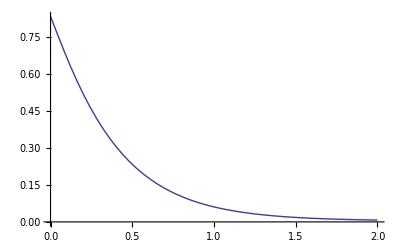

```mathematica
Plot[-ϵ(r),{r,0,2}]
```

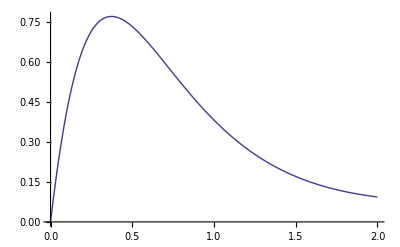

```mathematica
Plot[-2π r ϵ(r),{r,0,2}]
```

With a closed-form, one immediately can compute the asymptotic behaviour. For example, check the value of ϵ_x(0) by series expansion about r=0.

```mathematica
ϵ(r)+O[r]^3
```

-(515 π)/1944+(515 π r)/972+(r^2 (-784 π log(r)-784 ℽ π-1573 π+π log(6)+54 π log(3)+729 π log(2)))/2916+O(r^3)

Extending this computation for more than two closed shells is straightforward but tedious.

Pre-requisites

We modify Equal so that Listable operations are automatically applied to both sides of any equality:

```mathematica
Unprotect[Equal];
```

```mathematica
listableQ[f_]:=MemberQ[Attributes[f],Listable]
```

```mathematica
Equal/:lhs:f_Symbol?listableQ[___,_Equal,___]:=Thread[Unevaluated[lhs],Equal]
```

```mathematica
Protect[Equal];
```

Now, we can directly manipulate equations.

## References

[Reference] M Abramowitz and I Stegun, Handbook of Mathematical Functions, Dover, 1970 ⊳ http://www.convertit.com/Go/ConvertIt/Reference/AMS55.ASP

[Reference] The Wolfram Functions Site ⊳ http://functions.wolfram.com/